# Ejemplo de uso de Mathlink

Primero se carga el ejecutable

```mathematica
link = Install[FileNameJoin[{NotebookDirectory[],"bin","FreewayAC_Mathematica"}]]
```

LinkObject[…]

Las funciones diponibles son:

```mathematica
Column@LinkPatterns[link]
```

CreateCircularCA[size_Integer,vmax_Integer,density_Real,randp_Real,initVel_Integer]
CreateOpenCA[size_Integer,vmax_Integer,density_Real,randp_Real,initVel_Integer,newCarProb_Real,newCarSpeed_Integer]
CreateAutonomousCircularCA[size_Integer,vmax_Integer,density_Real,randp_Real,initVel_Integer,autDensity_Real]
CreateAutonomousOpenCA[size_Integer,vmax_Integer,density_Real,randp_Real,initVel_Integer,autDensity_Real,newCarProb_Real,newCarSpeed_Integer]
DeleteCA[]
CAStep[]
CAEvolve[iterations_Integer]
CACountCars[]
CACalculateOcupancy[]
CACalculateFlow[]
CAGetCurrent[]
CAGetHistory[]

Para crear un autómata celular primero hay que generarlo en la memoria del módulo

```mathematica
CreateAutonomousOpenCA[100,5,0.4,0.2,3,0.2,0.5,5]
```

Posteriormente se itera

```mathematica
CAEvolve[100]
```

y por último se cargan los datos a través de las funciones de comunicación: CACalculateOcupancy[], CACalculateFlow[], CAGetCurrent[] y CAGetHistory[]

```mathematica
ca = CAGetHistory[];
```

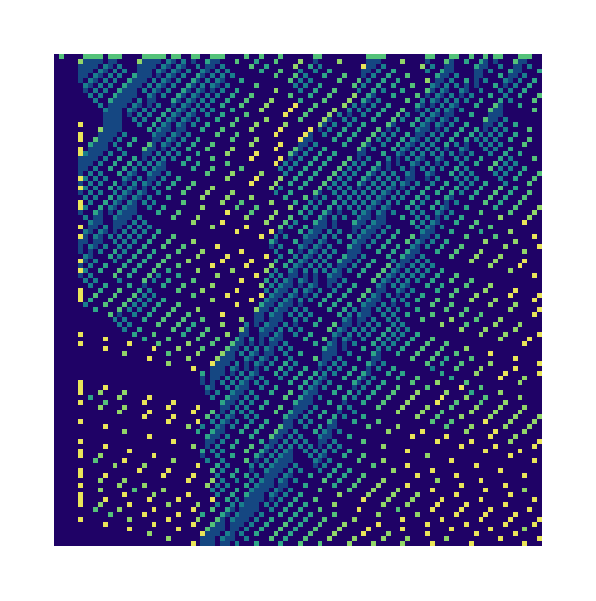

```mathematica
ArrayPlot[ca,ColorFunction->"BlueGreenYellow"]
```

## Animación

### Foto de cada iteración

```mathematica
CreateCircularCA[100,5,0.4,0.2,3];
CAEvolve[1000];
ca = CAGetHistory[];
```

```mathematica
colorRules = {
-1->White,
0->Black,
1->Blend[{Black,RGBColor[0., 0.25, 0.76]},0.2],
2->Blend[{Black,RGBColor[0., 0.25, 0.76]},0.4],
3->Blend[{Black,RGBColor[0., 0.25, 0.76]},0.6],
4->Blend[{Black,RGBColor[0., 0.25, 0.76]},0.8],
5->Blend[{Black,RGBColor[0., 0.25, 0.76]},1]
};
```

```mathematica
Manipulate[
ArrayPlot[
{ca[[i]]},
ColorFunction->"BlueGreenYellow",
ImageSize->1000,
ColorRules->colorRules
],
{i,1,Length[ca],1}
]
```

### Animación realista

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"AdvancedMapping.wl"}]]
```

```mathematica
FollowOneStep[caStep_,{position_Integer,_}]:=Block[{nextPos},
nextPos = position+Part[caStep,position];
If[nextPos>Length[caStep],
{nextPos-Length[caStep],-2},
If[nextPos == Length[caStep],
{nextPos,-2},
{nextPos,0}
]
]
];
OrbitOfVehicleAt[ca_,pos_]:=Block[{orbitRaw,processedDirty,toFlattenPos,processed},
orbitRaw = FoldList[FollowOneStep[#2,#1]&,{pos,0},ca];
processedDirty = SequenceReplace[orbitRaw,({{x_,0},{y_,-2}}/; x>y):>{{x,-2},{y,-2}}];
toFlattenPos = DeleteCases[Position[processedDirty,x_/;Depth[x]>2],{}];
processed = FlattenAt[processedDirty,toFlattenPos];
Return[processed];
];
CountVehicles[ca_]:=Length[Position[First[ca],x_/;x≠ -1]];
OrbitOfVehicleN[ca_,n_]:=Block[{initialVehiclePosition},
initialVehiclePosition = Flatten[Position[First[ca],x_/;x≠ -1]];
OrbitOfVehicleAt[ca,Part[initialVehiclePosition,n]]
];
```

```mathematica
CarsToPlot[ca_,t_]:=Block[{carImage,vehicles,coloredCars,vehicleOrbits,orbit},
carImage = ImageResize[-Graphics-,{100,200}];
vehicles = CountVehicles[ca];
coloredCars = Table[ImageRecolor[carImage,_->RandomColor[],Method->"Hue"],vehicles];
vehicleOrbits = ProgressTable[
orbit = OrbitOfVehicleN[ca,i];
{
0.5+Interpolation[orbit[[All,1]],InterpolationOrder->1][t],
Interpolation[orbit[[All,2]],InterpolationOrder->1][t]
},
{i,1,vehicles}
];

MapThread[Inset[#2,#1,Center,1]&,{vehicleOrbits,coloredCars}]
];
carsToPlot = CarsToPlot[ca,tt];
```

Animación de vehículos

```mathematica
DrawCar[t_]:=Graphics[
ReplaceAll[carsToPlot,tt->t],
PlotRange->{{-1,101},{-3,1}},
ImageSize->1500
];
```

```mathematica
Manipulate[DrawCar[t],{t,1,1000,0.01}]
```

```mathematica
AnimationAndArrayPlot[t_,height_ :130]:=Column[
{
DrawCar[t],
ArrayPlot[
Reverse[
If[t≤height,
PadLeft[Take[ca,{1,Floor[t]}],height,x]/.x->ConstantArray[-1,Length[First[ca]]],
Take[ca,{Floor[t]-height+1,Floor[t]}]
]
],
ImageSize->1530,
Frame->None,
ColorRules->colorRules
]
},
Spacings->0,
Alignment->Center
];
```

```mathematica
ExportName[file_,i_,total_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[total]];
directory = DirectoryName[file];
name = FileBaseName[file];
FileNameJoin[{directory,StringJoin[name,IntegerString[i,10,indexLength],".png"]}]
];
```

```mathematica
maxIter = 500;
interval = 0.1;
ProgressTable[
Export[ExportName[FileNameJoin[{NotebookDirectory[],"img","image.png"}],Floor[(t-1)/interval],Floor[(maxIter-1)/interval]],AnimationAndArrayPlot[t]],
{t,130,maxIter,interval}
];
```

```mathematica
Manipulate[AnimationAndArrayPlot[t],{t,1,200,0.01}]
```

Animación compacta de vehículos y grid

```mathematica
CompactAnimationAndArrayPlot[t_]:=Column[
{
DrawCar[t],
ArrayPlot[
{ca[[Floor[t]]]},
ImageSize->1530,
Mesh->All,
Frame->None,
ColorRules->colorRules
],
ArrayPlot[
Reverse[
If[t≤100,
Take[ca,{1,Floor[t]-1}],
Take[ca,{Floor[t]-100,Floor[t]-1}]
]
],
ImageSize->800,
Frame->None,
ColorRules->colorRules
]
},
Spacings->0,
Alignment->Center
];
```

```mathematica
Manipulate[CompactAnimationAndArrayPlot[t],{t,1,200,0.01}]
```